# 2D Linear System with Periodic Forcing

Jonathan Hahn
January 18, 2017

We are solving the following system:

x'[t] == -x[t] + R Sin[ω t]
y'[t] == ϵ(-y[t] + R Sin[ω t]

We want to know for what values of ω, R, and ϵ does the solution cross the line y = x - α.
This system has an attracting periodic orbit, so we will answer this problem for this limit cycle.
1. We want to know this for fixed R and ϵ, in what range of ω does the limit cycle cross y=x-α.
2. We want to prove that for some values of R, this range is 
3. If we fix ϵ, how does R affect this range of ω in which the limit cycle crosses y=x-α. 
4. How does the initial condition (x0, y0), affect the tipping range,  ω.

In more generality, we can consider linear matrix A with eigenvectors u, v, and eigenvalues -1, -ϵ
and consider the system:

x'[t] = A x[t] + (R Sin[t ω]
0)

5. And we ask for what parameters will x[t] cross the line y = -α.

```mathematica
DSolve[{x'[t] == -x[t] + R Sin[ω t],
y'[t] == ϵ(-y[t] + R Sin[ω t])},{x,y},t]
```

{{x→Function[{t},ⅇ^-t C[1]+(R (-ω Cos[t ω]+Sin[t ω]))/(1+ω^2)],y→Function[{t},ⅇ^(-t ϵ) C[2]+(R ϵ (-ω Cos[t ω]+ϵ Sin[t ω]))/(ϵ^2+ω^2)]}}

```mathematica
x[t_]=(R (-ω Cos[t ω]+Sin[t ω]))/(1+ω^2);
y[t_] = (R ϵ (-ω Cos[t ω]+ϵ Sin[t ω]))/(ϵ^2+ω^2);
```

## Excursion from equilibrium

```mathematica
A=R ω/(1+ω^2) - R ω ϵ^2/(ϵ^2 + ω^2);
B = R ω^2/(1+ω^2) - R ω^2 ϵ/(ϵ^2 + ω^2);
```

```mathematica
A^2 + B^2//FullSimplify
```

(R^2 (-1+ϵ)^2 ω^4)/((1+ω^2) (ϵ^2+ω^2))

```mathematica
Dist[R_,ϵ_,ω_] = (R (1-ϵ) ω)/Sqrt[2(1+ω^2) (ϵ^2+ω^2)]
```

(R (1-ϵ) ω)/(√2 √((1+ω^2) (ϵ^2+ω^2)))

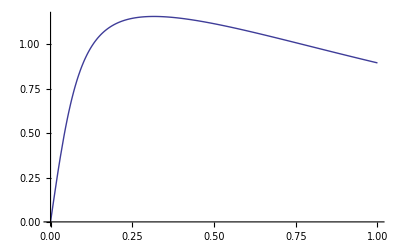

```mathematica
Plot[Dist[2,.1,ω],{ω,0,1},PlotRange->All]
```

```mathematica
Solve[D[Dist[1,ϵ,ω],ω]==0,ω]
```

{{ω→-√ϵ},{ω→-ⅈ √ϵ},{ω→ⅈ √ϵ},{ω→√ϵ}}

```mathematica
c=ContourPlot[Dist[1,ϵ,ω],{ϵ,0,1},{ω,0,5}];
```

```mathematica
p = Plot[Sqrt[ϵ],{ϵ,0,1}];
```

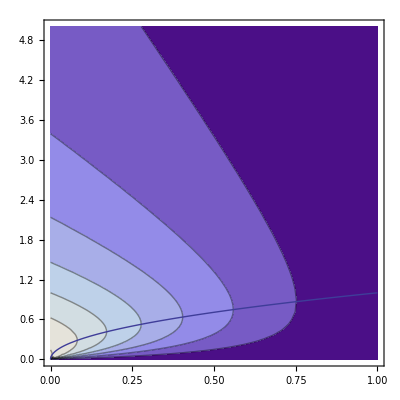

```mathematica
Show[c,p]
```